```mathematica
matheFunc[foto_]:=Module[{img,imgBin,imgFilt,imgEnhanced,edges,dilatedEdges,filledImage,componenti,misure},
SetDirectory[NotebookDirectory[]];
(*matheFunc usa funzioni di Mathematica*)
img=Import[foto];
img =ImageResize[img,Scaled[0.5]];
imgBin = Binarize[img];
imgFilt=GaussianFilter[imgBin,1];
imgEnhanced=ImageAdjust[imgFilt];
edges=EdgeDetect[imgEnhanced];
dilatedEdges=Dilation[edges,DiskMatrix[1]];
filledImage=FillingTransform[dilatedEdges];
componenti=MorphologicalComponents[filledImage];
(*Misurazioni,includendo "Shape" per ottenere contorni e bordi delle forme*)
misure=ComponentMeasurements[componenti,{"Centroid","BoundingBox","Orientation","Shape","Area","PerimeterLength","BoundingBoxArea","Eccentricity","Circularity","Rectangularity"}]]
```

```mathematica
simpleFunc[foto_]:=Module[{img,imgBin,imgFilt,imgEnhanced,edges,dilatedEdges,filledImage,componenti,misure},
SetDirectory[NotebookDirectory[]];
(* simpleFunc usa funzioni scritte e implementate a mano*)
img=Import[foto];
img =ImageResize[img,Scaled[0.5]];
imgBin = simpleBinarize[img];  (*funzione implementata sotto*)
imgFilt=GaussianFilter[imgBin,1];
imgEnhanced=ImageAdjust[imgFilt];
edges=EdgeDetect[imgEnhanced];
dilatedEdges=simpleDilation[edges,DiskMatrix[1]]; (*funzione implementata sotto*)
filledImage=simpleFillingTransform[dilatedEdges];(*funzione implementata sotto*)
componenti=MorphologicalComponents[filledImage];
(*Misurazioni,includendo "Shape" per ottenere contorni e bordi delle forme*)
misure=ComponentMeasurements[componenti,{"Centroid","BoundingBox","Orientation","Shape","Area","PerimeterLength","BoundingBoxArea","Eccentricity","Circularity","Rectangularity"}]]
```

```mathematica
simpleBinarize[img_Image]:=Module[{gray,data,thresh,binaryData,dataElement},

gray=ColorConvert[img,"Grayscale"];(*conversione dei colori in scala di grigi*)
data=ImageData[gray];(* restituisce un array(Matrice) di pixel dall' immagine gray*)
thresh=Mean[Flatten[data]]; (*Determina come accedere all'elemento dati in base alle dimensioni di'data'*)
(*restituisce la media stimata degli elementi in data*)

If[Length[Dimensions[data]]==3, (*inserito per poter valutare sia PNG che JPG*)
dataElement=#[[1]]&,(*Per array 3D (es.PNG problematici):usa #[[1]]*)
dataElement=#&       (*Per array 2D (es.JPG,PNG standard):usa # direttamente*)];

(*Applica la binarizzazione usando la funzione di accesso'dataElement'*)
binaryData=Map[If[dataElement[#]>thresh,1,0]&,data,{2}]; (* se l' elemento è maggiore della media allora elemento impostato a 1(bianco)  {2}-> fatto a livello 2*)
Image[binaryData,"Bit"]]
```

```mathematica
simpleDilation[img_Image,se_?MatrixQ]:=Module[{data,dims,seDims,offset,padded,result,window},
data=ImageData[img];
dims=Dimensions[data];
seDims=Dimensions[se];
(*Calcola l'offset per il padding (per gestire i bordi)*)
offset=Floor[seDims/2];
(*Aggiunge un padding di zeri intorno all'immagine*)
padded=ArrayPad[data,offset,0];
(*Applica l'operazione di dilatazione per ogni pixel*)
result=Table[
window=padded[[i;;i+seDims[[1]]-1,j;;j+seDims[[2]]-1]];
(*Estrae una finestra da padded della stessa dimensione della matrice strutturante*)

If[Max[window*se]==1,1,0],{i,1,dims[[1]]},{j,1,dims[[2]]}
(*Dato che il padding ha "larghezza" seDims/2, la finestra risulta sempre centrata sul pixel data[[i,j]].*)
];

Image[result,"Bit"]
];
```

```mathematica
simpleFillingTransform[img_Image]:=Module[{data,dims,compImg,binImg,comp,borderIDs,holeMask,filledData},(*Estrae la matrice dei pixel dall'immagine binaria*)
data=ImageData[img];
dims=Dimensions[data];
(*Crea l'immagine complementare:inverte i valori (0↔1)*)
compImg=1-data;
(*Converte compImg in un'immagine binaria e calcola le componenti connesse.*)
binImg=Binarize[Image[compImg]];
comp=MorphologicalComponents[binImg];
(*Identifica gli ID delle componenti che toccano il bordo dell'immagine*)
borderIDs=DeleteDuplicates[
Flatten[{
comp[[1,All]],(*prima riga*)
comp[[dims[[1]],All]],(*ultima riga*)
comp[[All,1]],(*prima colonna*)
comp[[All,dims[[2]]]]  (*ultima colonna*)
}]
];(*scopo : identificare quali componenti non devoono essere riempite perchè connesse a esterno*)
holeMask=Map[If[#!=0&&Not[MemberQ[borderIDs,#]],1,0]&,comp,{2}]; (*#!=0 significa # con ID != 0 cioè non lo sfondo*)

filledData=MapThread[Max[#1,#2]&,{data,holeMask},2]; (*OR pixel a pixel, sommo edges + hole mask*)
(*ricostruisce l'immagine binaria riempita*)
Image[filledData,"Bit"]];
```

Mathe starting

Prestazioni Mathe: 
 Media per singolo frame: 0.106205
 Tempo massimo per singolo frame:  0.112443
 Tempo minimo per singolo frame:  0.100138
 Tempo totale per 100 frame:  1.062046

Simple starting

Prestazioni simple: 
 Media per singolo frame: 1.599773
 Tempo massimo per singolo frame:  1.621662
 Tempo minimo per singolo frame:  1.586083
 Tempo totale per 100 frame:  15.998729

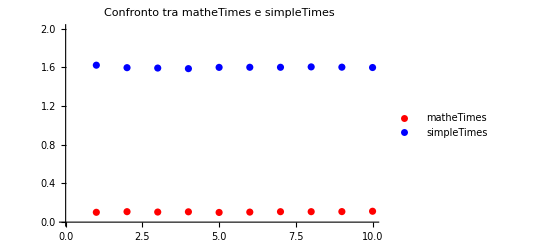

```mathematica
(*Valutazione prestazioni*)

SetDirectory[NotebookDirectory[]];
foto ="foto5.jpg";
matheTimes={};
simpleTimes={};
Print["Mathe starting"];
tot = AbsoluteTime[];
For[i=0,i<10,i++,
time = AbsoluteTime[];
matheFunc[foto];
timer = AbsoluteTime[]-time;
AppendTo[matheTimes,timer];
];
totm = AbsoluteTime[]-tot;

Print["Prestazioni Mathe: \n Media per singolo frame: ",Mean[matheTimes] ,"\n Tempo massimo per singolo frame:  ",
Max[matheTimes],"\n Tempo minimo per singolo frame:  ",
Min[matheTimes],"\n Tempo totale per 100 frame:  ", totm];

Print["Simple starting"];
tot = AbsoluteTime[];
For[i=0,i<10,i++,
times = AbsoluteTime[];
simpleFunc[foto];
timers =AbsoluteTime[]-times;
AppendTo[simpleTimes,timers];
];
tots = AbsoluteTime[]-tot;



Print["Prestazioni simple: \n Media per singolo frame: ",Mean[simpleTimes] ,"\n Tempo massimo per singolo frame:  ",
 Max[simpleTimes],"\n Tempo minimo per singolo frame:  ",
Min[simpleTimes],"\n Tempo totale per 100 frame:  ", tots];

ListPlot[{matheTimes,simpleTimes},PlotLegends->{"matheTimes","simpleTimes"},PlotStyle->{Red,Blue},PlotLabel->"Confronto tra matheTimes e simpleTimes",PlotRange->{{Automatic,Automatic},{0,2}}]
```